## Объявление глобальных переменных

```mathematica
SetDirectory["/Users/kirillivanov/Documents/Code/For Geant analysis/a-fe_g-xe/"]
print@x_:=(Print@x;x);
grids[dist_]:=Table[If[OddQ@Round@(i/dist),{i,Dashed},{i}],{i,Ceiling@(#1/dist)*dist,Floor@(#2/dist)*dist,dist}]&;
Needs@"ErrorBarPlots`";
dropLastDot@string_:=If[StringTake[string,-1]===".",StringDrop[string,-1],string];
vertSize=0.0001;horizSize=0.0001;
vertCross[coord1_,coord2_]:={Line@{coord1,coord2},Line/@({{#1+vertSize,#2},{#1-vertSize,#2}}&@@@{coord1,coord2})};
horizCross[coord1_,coord2_]:={Line@{coord1,coord2},Line/@({{#1,#2+horizSize},{#1,#2-horizSize}}&@@@{coord1,coord2})};
```

/Users/kirillivanov/Documents/Code/For Geant analysis/a-fe_g-xe

## Построение одного графика

### Импорт табличных данных

```mathematica
data = Import["log.csv"];
data//TableForm
```

Energy, MeV | Sigma(E), MeV | E_gap, MeV | Sigma(E_gap), MeV
500. | 0. | 5.9954 | 0.0662105
1000. | 0. | 12.9879 | 0.106172
2000. | 0. | 27.1413 | 0.145696
3000. | 0. | 41.6524 | 0.175948
4000. | 0. | 55.4678 | 0.223755
5000. | 0. | 69.7438 | 0.230343
6000. | 0. | 83.6097 | 0.271372
7000. | 0. | 98.0061 | 0.289905
8000. | 0. | 111.926 | 0.303556
9000. | 0. | 126.036 | 0.321278
10000. | 0. | 140.273 | 0.359092

### Фитирование табличных данных линейной функцией

В первый столбец “data” указывается величина по оси x, во второй – по y.

FittedModel[-1.11047+0.0141808 x-5.13488×10^-9 x^2]

| Estimate | Standard Error | t-Statistic | P-Value
1 | -1.11047 | 0.119038 | -9.32877 | 0.0000142241
x | 0.0141808 | 0.0000550871 | 257.424 | 5.80541×10^-17
x^2 | -5.13488×10^-9 | 5.19311×10^-9 | -0.988786 | 0.351727

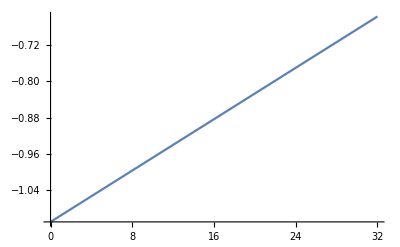

```mathematica
forFit=data⟦2;;,{1,3}⟧;
forFitCr=data⟦2;;,-1⟧;
fit2=LinearModelFit[forFit,{1,x, x^2},x]
fit2@"ParameterTable"
Plot[fit2["Function"]@x, {x, 0, 32}]
```

```mathematica
((print@fit2["FitResiduals"])/(print@forFitCr))^2
χ22=Total[(fit2["FitResiduals"]/forFitCr)^2]/(11-3)
```

{0.016781,-0.0772784,-0.0892382,0.266817,-0.062594,0.0788553,-0.179502,0.102906,-0.0813506,-0.0644497,0.0890535}

{0.0662105,0.106172,0.145696,0.175948,0.223755,0.230343,0.271372,0.289905,0.303556,0.321278,0.359092}

{0.0642364,0.529777,0.375151,2.29964,0.0782562,0.117196,0.437531,0.126,0.0718195,0.040242,0.0615021}

0.525168

### Построение графика линейной функции + табличные данные с крестами погрешностей

В переменную “data” указываются табличные данные в формате “{столбец данных оси х, столбец данных оси y, погрешность данных оси х, погрешность данных оси y}.
В случае, если нужна погрешность только по одной оси, в “data” ненужной оси записывается произвольный столбец, а в коде ниже соответствующие “Cross” закомменчиваются.
В переменную “fit” указывается отфитированная выше функция, соответствующая этим табличным данным.

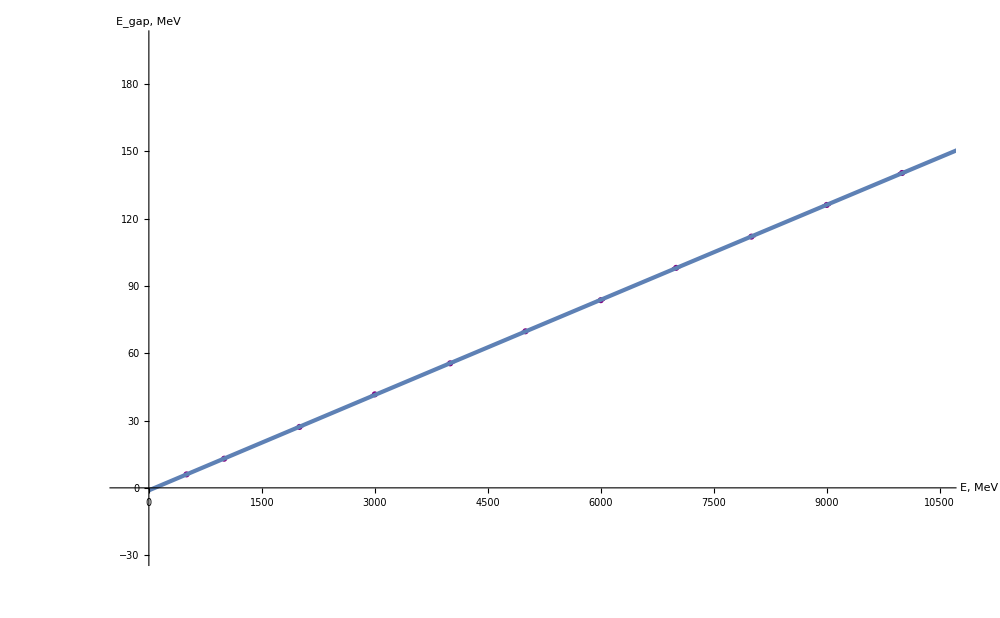

images/png/calib2.png

images/png/fit_res2.png

```mathematica
plot2 =Show[ErrorListPlot[{{#1,#2},ErrorBar@##3}&@@@data⟦2;;,{1,3,2,4}⟧,
GridLines->{grids@500,grids@50},
AxesLabel->(Style[#,Bold,Black,Large]&)/@{"E, MeV","E_gap, MeV"},
AxesStyle->Directive[Large,Black],PlotMarkers->Automatic,PlotStyle-> Purple,ImageSize->1000,
ErrorBarFunction->Function[{coords,errors},{Thickness@0.006,
vertCross@@({{#1,#2+errors⟦2,1⟧},{#1,#2+errors⟦2,2⟧}}&@@coords),
horizCross@@({{#1+errors⟦1,1⟧,#2},{#1+errors⟦1,2⟧,#2}}&@@coords)
}],
(*Ticks->{myTicksX,myTicksY},*)
PlotRange->{{-300,10500},{-30,199}}], 
Plot[fit2["Function"]@x,{x,0,10900}, PlotStyle->Thickness@0.003]]
Export["images/png/calib2.png",plot2,"PNG"]
Export["images/png/fit_res2.png",fit2@"ParameterTable","PNG"]
```

#### Экспорт фита данных в CSV формат

```mathematica
exportE = {fit2@"BestFitParameters",fit2@"ParameterErrors",χ22}
Export["fit_res2.csv",exportE,"CSV"]
```

{{-1.11047,0.0141808,-5.13488×10^-9},{0.119038,0.0000550871,5.19311×10^-9},0.525168}

fit_res2.csv

## Построение одного графика

### Импорт табличных данных

```mathematica
dataR = Import["log_red.csv"];
dataR//TableForm
```

Energy, MeV | Sigma(E), MeV | dE/E | Sigma(dE/E)
880.363 | 8.84368 | 0.243618 | 0.00520122
1364.8 | 10.9467 | 0.201398 | 0.00407093
1907.86 | 12.6936 | 0.168673 | 0.00334835
2939.06 | 16.6742 | 0.139439 | 0.00269058
3530.49 | 17.1783 | 0.125176 | 0.00238798
4119.33 | 20.4426 | 0.119731 | 0.0022958
5037.89 | 21.8131 | 0.108123 | 0.00203791
6328.21 | 25.5376 | 0.0978351 | 0.00183446
7157.45 | 25.0875 | 0.0941503 | 0.00175583
7996.04 | 26.8442 | 0.0845152 | 0.00157871
9787.33 | 31.0485 | 0.0791267 | 0.00146684

### Фитирование табличных данных линейной функцией

В первый столбец “data” указывается величина по оси x, во второй – по y.

FittedModel[0.00909037+7.00896/(√x)]

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.00909037 | 0.00152497 | 5.96101 | 0.000212439
1/(√x) | 7.00896 | 0.080146 | 87.4524 | 1.6937×10^-14

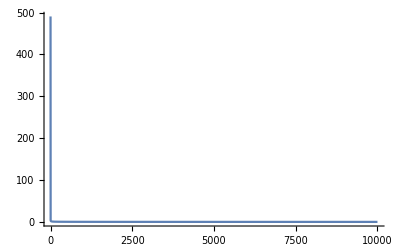

```mathematica
forFitR=dataR⟦2;;,{1,3}⟧;
fitR=LinearModelFit[forFitR,{1,1/Sqrt[x]},x]
forFitCrR=dataR⟦2;;,-1⟧;
fitR@"ParameterTable"
Plot[fitR["Function"]@x, {x, 0, 10000}, PlotRange->All]
```

```mathematica
((print@fitR["FitResiduals"])/(print@forFitCrR))^2
χR=Total[(fitR["FitResiduals"]/forFitCrR)^2]/(11-2)
```

{-0.00169577,0.00258554,-0.000882103,0.0010633,-0.0018744,0.0014365,0.00028426,0.000637169,0.00221339,-0.0029572,-0.000810685}

{0.00520122,0.00407093,0.00334835,0.00269058,0.00238798,0.0022958,0.00203791,0.00183446,0.00175583,0.00157871,0.00146684}

{0.106297,0.403381,0.0694029,0.156177,0.616119,0.391509,0.0194562,0.12064,1.5891,3.50879,0.30545}

0.809592

### Построение графика линейной функции + табличные данные с крестами погрешностей

В переменную “data” указываются табличные данные в формате “{столбец данных оси х, столбец данных оси y, погрешность данных оси х, погрешность данных оси y}.
В случае, если нужна погрешность только по одной оси, в “data” ненужной оси записывается произвольный столбец, а в коде ниже соответствующие “Cross” закомменчиваются.
В переменную “fit” указывается отфитированная выше функция, соответствующая этим табличным данным.

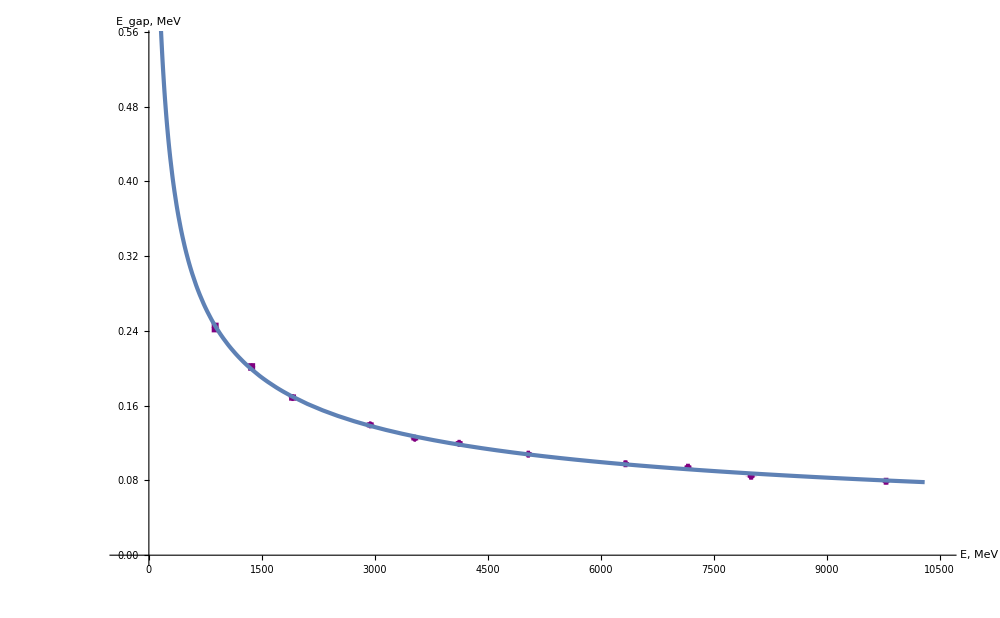

images/png/re.png

images/png/fit_re_res.png

```mathematica
plotR=Show[ErrorListPlot[{{#1,#2},ErrorBar@##3}&@@@dataR⟦2;;,{1,3,2,4}⟧,
GridLines->{grids@500,grids@0.05},
AxesLabel->(Style[#,Bold,Black,Large]&)/@{"E, MeV","E_gap, MeV"},
AxesStyle->Directive[Large,Black],PlotMarkers->Automatic,PlotStyle-> Purple,ImageSize->1000,
ErrorBarFunction->Function[{coords,errors},{Thickness@0.005,
vertCross@@({{#1,#2+errors⟦2,1⟧},{#1,#2+errors⟦2,2⟧}}&@@coords),
horizCross@@({{#1+errors⟦1,1⟧,#2},{#1+errors⟦1,2⟧,#2}}&@@coords)
}],
(*Ticks->{myTicksX,myTicksY},*)
PlotRange->{{-300,10500},{0,0.55}}], 
Plot[fitR["Function"]@x,{x,0,10300}, PlotStyle->Thickness@0.003, PlotRange->Full]]
Export["images/png/re.png",plotR,"PNG"]
Export["images/png/fit_re_res.png",fitR@"ParameterTable","PNG"]
```

#### Экспорт фита данных в CSV формат

```mathematica
exportR = {fitR@"BestFitParameters",fitR@"ParameterErrors",χR}
Export["fit_re_res.csv",exportR,"CSV"]
```

{{0.00909037,7.00896},{0.00152497,0.080146},0.809592}

fit_re_res.csv